```mathematica
database = Import[FileNameJoin[{NotebookDirectory[],"sp500v2.wdx"}]];
```

```mathematica
First[database]//Keys
```

{Name,Symbol,Sector,FirstDate,LastDate,Dates,Prices,Returns,DatedPrices,DatedReturns}

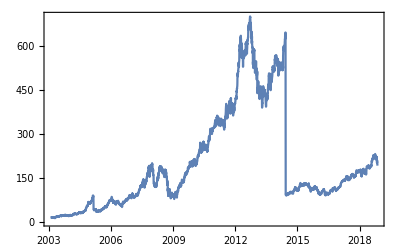
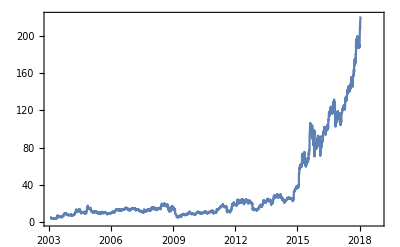
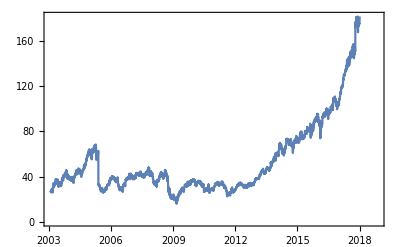
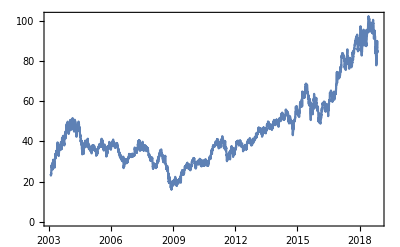
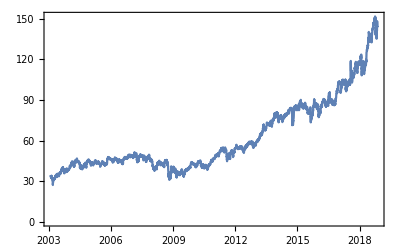
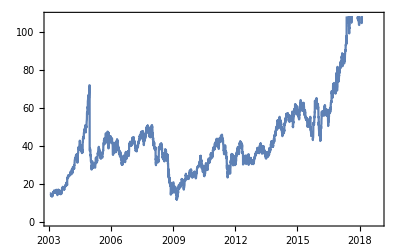
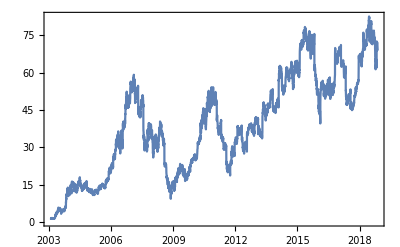
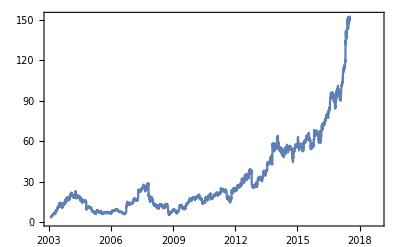

```mathematica
Map[DateListPlot,Take[database[[All,"DatedPrices"]],20]]
```